# Assignment 9 - W8

## Cameron Embree, worked with Allie

```mathematica
data=Import["http://www.nhl.com/ice/teamstats.htm?season=20122013&gameType=2&viewName=summary","Data"];
```

```mathematica
colID=data[[4,2,3,2]] (* column data names *)
extDat=data[[4,2,3,4]]; (* the data by row based on team *)
```

{Team,GP,W,L,OT,P,ROW,HROW,RROW,P%,G/G,GA/G,5-5 F/A,PP%,PK%,S/G,SA/G,Sc 1%,Tr 1st%,Ld 1%,Ld 2%,OS%,OSB%,FO%}

```mathematica
aa={#[[11]],#[[12]],#[[4]],#[[19]],#[[8]],#[[22]]}&/@extData

{u,w,v}=SingularValueDecomposition[aa];
w//MatrixForm
```

{{0.802,3.1,36,0.897,30,0.897},{0.75,3.38,36,0.806,33,0.95},{0.688,2.79,30,0.75,24,0.895},{0.656,3.04,29,0.724,26,0.81},{0.625,2.58,29,0.793,24,0.905},{0.646,2.65,28,0.731,24,0.652},{0.615,2.73,27,0.808,25,0.864},{0.594,3.04,27,0.654,24,0.864},{0.615,2.54,26,0.645,21,0.783},{0.594,3.02,26,0.594,26,0.87},{0.583,2.62,26,0.857,22,1.},{0.573,2.46,26,0.783,22,0.9},{0.594,2.42,25,0.8,17,0.833},{0.583,2.33,25,0.72,21,0.905},{0.583,2.54,24,0.64,22,0.857},{0.573,2.4,24,0.6,19,1.},{0.573,2.81,24,0.739,20,0.842},{0.531,2.62,24,0.696,22,0.9},{0.51,2.75,23,0.692,22,0.85},{0.5,2.67,22,0.696,20,0.706},{0.531,2.52,21,0.737,17,0.938},{0.5,2.46,21,0.667,14,0.692},{0.5,2.29,19,0.737,17,0.75},{0.469,2.56,19,0.5,17,0.75},{0.438,2.65,19,0.579,18,0.933},{0.438,2.67,19,0.6,19,0.8},{0.417,3.06,18,0.684,17,0.786},{0.427,2.27,16,0.611,14,0.8},{0.406,2.38,16,0.563,14,0.643},{0.375,2.27,15,0.647,12,0.857}}

(178.517 | 0. | 0. | 0. | 0. | 0.
0. | 7.34664 | 0. | 0. | 0. | 0.
0. | 0. | 2.40823 | 0. | 0. | 0.
0. | 0. | 0. | 0.590769 | 0. | 0.
0. | 0. | 0. | 0. | 0.34407 | 0.
0. | 0. | 0. | 0. | 0. | 0.116642
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

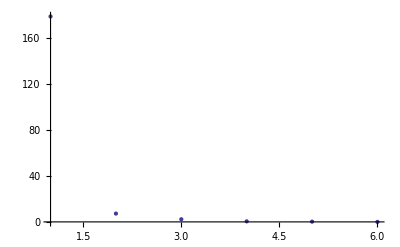

```mathematica
ListPlot[Diagonal[w],PlotRange->All]
```

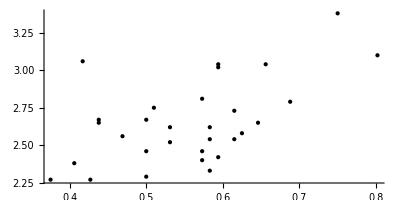

```mathematica
(* Two dimentional graph *)
Graphics[Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{extDat[[All,2]],u.w.Transpose[v[[1;;2]]]}],Axes->True, AspectRatio->.5]
```

```mathematica
(* Three dimentional graph *)
Graphics3D[Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{extDat[[All,2]],u.w.Transpose[v[[1;;3]]]}],Axes->True, AspectRatio->1]
```

-Graphics3D-